```mathematica
$MachineName
```

maincluster

## Init

```mathematica
(*EINZIG PATH*)
```

```mathematica
rawPass=StringSplit[raw,"\n"][[3073;;456563]];
```

```mathematica
456563-3073
```

453490

```mathematica
Length@rawPass==453491
```

True

```mathematica
id=Map[StringSplit[#,":"]&,rawPass][[;;,1]];
```

```mathematica
usrName=Table[StringSplit[rawPass[[n]],":"][[2]],{n,453491}];
```

```mathematica
psk=Map[If[Length[#]>=3,#[[3]],""]&,StringSplit[#,":"]&/@rawPass];
```

## Functions

```mathematica
elementAnalysis[pskList_]:=Module[{charGroups},charGroups=Flatten@StringCases[pskList,{DigitCharacter->"Numbers",LetterCharacter->"Letters",Except[DigitCharacter|LetterCharacter]->"Others"}];
Counts[charGroups]]
```

```mathematica
datePatternAnalysis[pskList_]:=Module[{dateFormats},
patterns={"Year","Month","Day"};

]
```

```mathematica
englishWordAnalysis[pskList_]:=Module[{words},words=Select[pskList,DictionaryLookup[#]!={}&];
Tally[words]]
```

```mathematica
keyboardRows={"1234567890-=","qwertyuiop[]","asdfghjkl;'","zxcvbnm,./"};
```

```mathematica
keyboardAdjacency=StringCases[keyboardRows,x__/;StringLength[x]>=6,Overlaps->All];
```

```mathematica
keyboardAdjacencyAnalysis[psk_List]:=Select[psk,StringContainsQ[keyboardAdjacency]]
```

## Calling

### Element Analysis

```mathematica
eA=elementAnalysis[psk];
```

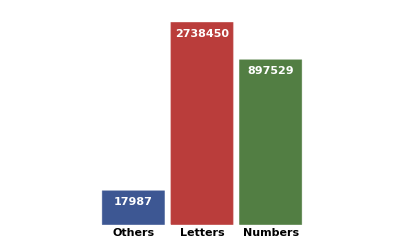

```mathematica
BarChart[eA,
ColorFunction->ColorData["DarkRainbow"],
ScalingFunctions->"Log",
ChartLabels->Placed[(Style[#,Black,Larger,Bold]&/@{"Others","Letters","Numbers"}),Below],
Axes->False,
ImageSize->400,
LabelingFunction->Top,
LabelStyle->Directive[Bold,White,Larger],
Background->White
]
```

```mathematica
lenSortPsk=SortBy[psk,StringLength];
```

```mathematica
lenSortPskList=Gather[lenSortPsk,StringLength[#1]==StringLength[#2]&];
```

```mathematica
combinationsEz=Flatten[StringCases[#,
{StartOfString~~x:DigitCharacter..~~EndOfString:>"onlyNumbers",
StartOfString~~n:DigitCharacter..~~x:LetterCharacter..~~EndOfString:>("num+letter"),
StartOfString~~x:LetterCharacter..~~EndOfString:>"onlyLetters",
StartOfString~~n:LetterCharacter..~~x:DigitCharacter..~~EndOfString:>("letter+num"),
StartOfString~~DigitCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"num+others",
StartOfString~~LetterCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"letter+others",
StartOfString~~""~~EndOfString:>"noPsk"}]/.{}->{"NotMatched"}]&/@lenSortPskList;
```

```mathematica
combinations=StringCases[lenSortPsk,
{StartOfString~~x:DigitCharacter..~~EndOfString:>"onlyNumbers@"<>ToString@StringLength[x],
StartOfString~~n:DigitCharacter..~~x:LetterCharacter..~~EndOfString:>("num@"<>ToString@StringLength[n]<>"+letter@"<>ToString@StringLength[x]),
StartOfString~~x:LetterCharacter..~~EndOfString:>"onlyLetters@"<>ToString@StringLength[x],
StartOfString~~n:LetterCharacter..~~x:DigitCharacter..~~EndOfString:>("letter@"<>ToString@StringLength[n]<>"+num@"<>ToString@StringLength[x]),
StartOfString~~DigitCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"num+others",
StartOfString~~LetterCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"letter+others",
StartOfString~~""~~EndOfString:>"noPsk"}]/.{}->{"NotMatched"};
```

```mathematica
combinationsEzData=KeyValueMap[#1->#2&,Reverse[Sort[Counts[#]]]]&/@combinationsEz;
```

```mathematica
toCallOut[x_]:=Map[Callout[#[[2]],#[[1]]]&,x,{2}]
```

```mathematica
sel=Select[combinationsEzData,Total[#[[;;,2]]]>40000&];
head=DeleteDuplicates[Flatten@sel[[;;,;;,1]]];
```

```mathematica
drColor=Reverse[ColorData["DarkRainbow"]/@Array[#&,7,{0,1}]];
colorLabel[x_]:=drColor[[First@@Position[head,x]]];
```

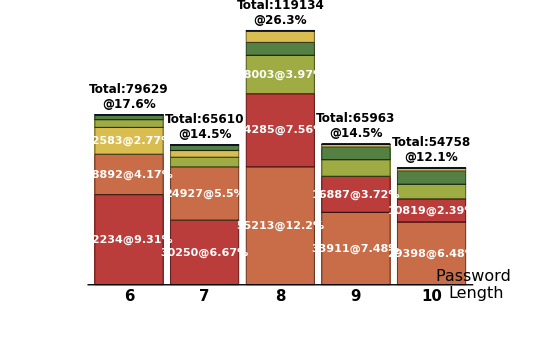

```mathematica
Legended[BarChart[Map[
Labeled[
Style[#[[2]],colorLabel[#[[1]]]],
Style[
If[#[[2]]>10000,ToString[#[[2]]]<>"@"<>ToString[NumberForm[#[[2]]/Length[psk] 100.,3]]<>"%",""],Bold,White,Larger

],Center]&,
sel,{2}],
ChartLayout->"Stacked",
(*ImagePadding->{{100,100},{0,0}},*)
ImageSize->550,
Axes->{True,False},
AxesLabel->{Style["Password \nLength",Black,16,FontFamily->"Times"],Style["Number",Bold,FontFamily->"Arial"]},
ChartLabels->{Placed[{Style[ToString[#],Bold,15]&/@Range[6,10],Style["Total:"<>ToString[#]<>"\n@"<>ToString[NumberForm[#/Length[psk] 100.,3]]<>"%",Bold,12]&/@Total[sel[[;;,;;,2]]ᵀ]},{Below,Above}],Placed[{""},Top]},
AxesStyle->Directive[Black,Larger],

Background->White

]
,Column[Table[Row[{drColor[[i]],Style[head[[i]],Black,16,FontFamily->"Times"]}],{i,Length@head}]]
]
```

### Character Analysis

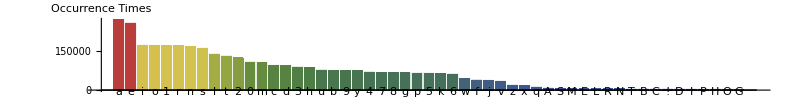

```mathematica
BarChart[Select[CharacterCounts[StringJoin[psk]],#>3000&],
ChartLabels->Automatic,
AspectRatio->1/8,
Background->White,
ImageSize->1000,
ColorFunction->ColorData["DarkRainbow"],
LabelStyle->Directive[Black,Bold,15,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 16],
AxesLabel->"Occurrence\nTimes"

]
```

```mathematica
azLower=Lookup[CharacterCounts[StringJoin[psk]],CharacterRange["a","z"]];
azUpper=Lookup[CharacterCounts[StringJoin[psk]],CharacterRange["A","Z"]];
```

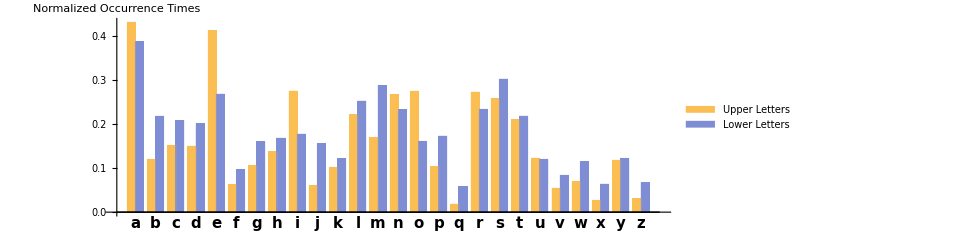

```mathematica
BarChart[{Normalize@azLower,Normalize@azUpper}ᵀ,
BarSpacing->{0,.5},
AspectRatio->1/3,
ImageSize->800,
ChartLabels->{Placed[CharacterRange["a","z"],Below],None},
ChartLegends->{"Upper Letters","Lower Letters"},
LabelStyle->Directive[Black,Bold,15,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 16],
AxesLabel->"Normalized\nOccurrence Times"

]
```

### Length Analysis

```mathematica
lengthMap=KeyValueMap[#1->#2&,Counts[StringLength/@psk]];
rangeCtrl={x==0,0<x<=6,6<x<=10,10<x<=14,x>14};
```

```mathematica
rangeLength=Map[lengthMap[[Flatten@Position[lengthMap,(x_->y_)/;#]]]&,rangeCtrl];
```

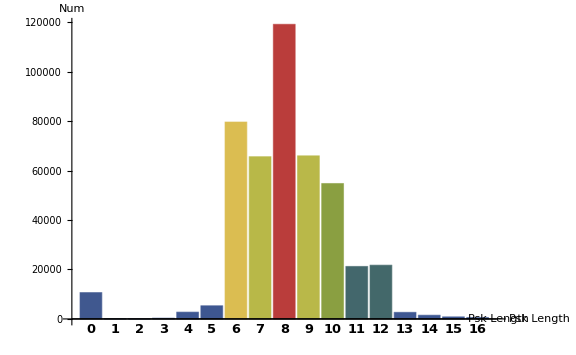

```mathematica
BarChart[SortBy[KeyValueMap[#1->#2&,Counts[StringLength/@psk]],#1&][[;;17,2]],
ColorFunction->ColorData["DarkRainbow"],
ChartLabels->Placed[Range[0,16],Below],
ImageSize->Large,
LabelStyle->Directive[Black,Bold,13,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 13],
AxesLabel->{"\nPsk Length","Num"}
]
```

### Date Analysis

```mathematica
digit6=Flatten@StringCases[psk,Repeated[DigitCharacter,{6}]];
digit8=Flatten@StringCases[psk,Repeated[DigitCharacter,{8}]];
```

```mathematica
Off[FromDateString::str]
Off[FromDateString::ambig]
```

```mathematica
Date1Q[str_]:=StringMatchQ[str,DatePattern[{"Month","Day","Year"}]|DatePattern[{"Day","Month","Year"}]|DatePattern[{"Year","Month","Day"}]]
```

```mathematica
Pick[psk,ResourceFunction["MonitorProgress"]@Map[Date1Q[#]&,psk],True]
```

{2/17/55,2-18-07,1-22-1,10-03-98,4/24/1989,12/17/87,20.09.1974,9/2/82,12/31/1972,5-10-1955,09.29.1987,11-07-1982}

```mathematica
dateStringSeparate6[str_]:=StringCases[str,StartOfString~~a1:Repeated[DigitCharacter,{2}]~~a2:Repeated[DigitCharacter,{2}]~~a3:Repeated[DigitCharacter,{2}]:>a1<>"-"<>a2<>"-"<>a3];
dateStringSeparate8[str_]:=StringCases[str,StartOfString~~a1:Repeated[DigitCharacter,{2}]~~a2:Repeated[DigitCharacter,{2}]~~a3:Repeated[DigitCharacter,{4}]:>a1<>"-"<>a2<>"-"<>a3];
```

```mathematica
digit6S=Flatten[dateStringSeparate6[#]&/@digit6];
digit8S=Flatten[dateStringSeparate6[#]&/@digit8];
```

```mathematica
susDate=Join[Select[digit6S,Date1Q[#]&],Select[digit8S,Date1Q[#]&]];
```

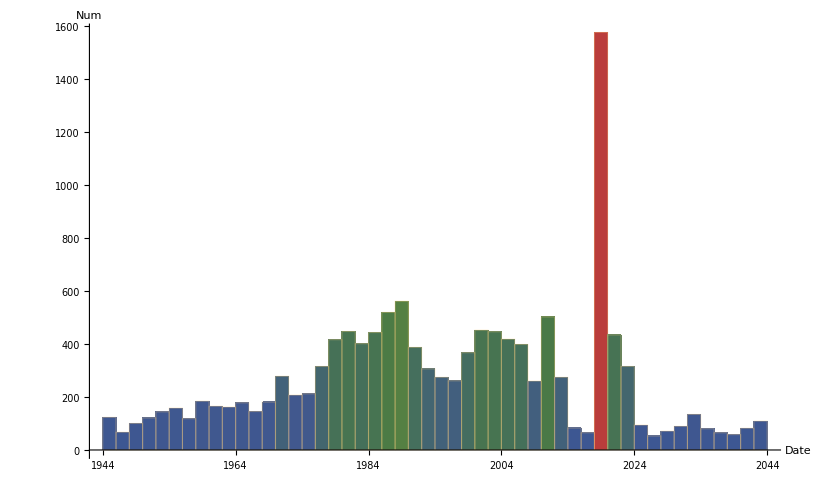

```mathematica
DateHistogram[FromDateString[susDate],
ColorFunction->ColorData["DarkRainbow"],
ImageSize->Large,
LabelStyle->Directive[Black,Bold,13,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 13],
AxesLabel->{"\nDate","Num"}

]
```

```mathematica
weakDigits=Reverse@Sort@Select[Counts[Flatten@StringCases[psk,Repeated[DigitCharacter,{4,Infinity}]]],#>100&];
```

```mathematica
weakDigitsKey=KeyValueMap[#1->#2&,weakDigits];
```

```mathematica
susYearStr=Cases[weakDigitsKey[[;;,1]],x_/;(ToExpression[x]>1800&&ToExpression[x]<2024):>x];
```

```mathematica
susDateRemainningsMDY=
Flatten@
StringCases[
Select[
Flatten[
StringCases[
psk,
Repeated[DigitCharacter,{8}]
]
],
StringContainsQ[#,susYearStr]&
],
{__~~susYearStr~~EndOfString}
];
susDateRemainningsYMD=
Flatten@
StringCases[
Select[
Flatten[
StringCases[
psk,
Repeated[DigitCharacter,{8}]
]
],
StringContainsQ[#,susYearStr]&
],
{StartOfString~~susYearStr~~__}
];
```

```mathematica
susDateMDY=Flatten@StringCases[
Flatten@Map[dateStringSeparate8[#]&,susDateRemainningsMDY],
DatePattern[{"Month","Day","Year"}]
];
```

```mathematica
susDateYMD=Flatten@StringCases[
Flatten@Map[dateStringSeparate8[#]&,susDateRemainningsYMD],
DatePattern[{"Month","Day","Year"}]
];
```

```mathematica
susDateFin=Join[FromDateString[susDateMDY,{"Month","Day","Year"}],FromDateString[susDateYMD,{"Year","Month","Day"}]];
```

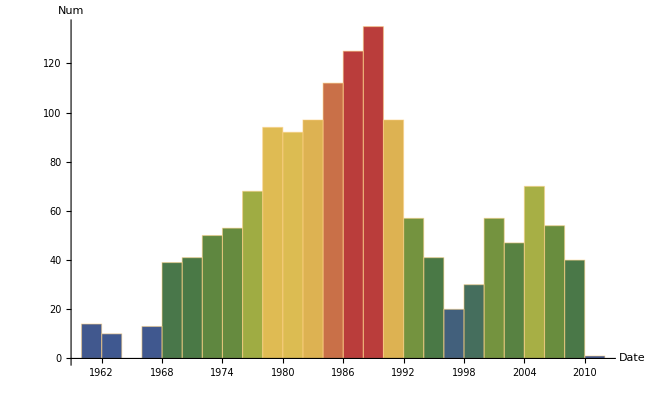

```mathematica
DateHistogram[susDateFin,
ColorFunction->ColorData["DarkRainbow"],
ImageSize->Large,
LabelStyle->Directive[Black,Bold,13,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 13],
AxesLabel->{"\nDate","Num"}
]
```

### Weak Digit Password

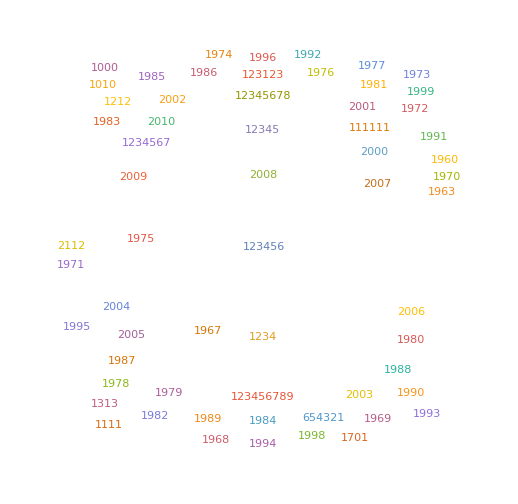

```mathematica
WordCloud[weakDigits]
```

### Word Analysis

```mathematica
engAnalysis=englishWordAnalysis[psk];
```

```mathematica
mostWords=Sort[engAnalysis,#1[[2]]>=#2[[2]]&][[;;100]];
```

```mathematica
wc=WordCloud[mostWords];
```

```mathematica
TableForm[{Dataset[mostWords[[;;15]]],wc},TableDirections->Row]
```

以下为所有密码中含有有意义英文单词的频率

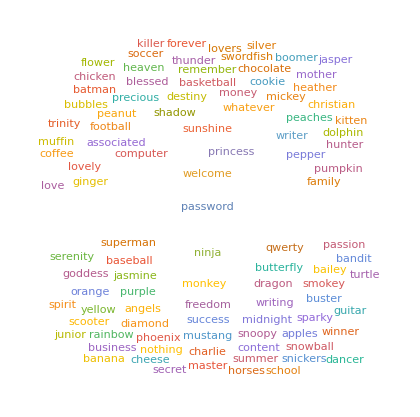
| -Graphics-

### Keyboard Analysis

```mathematica
keyAnalysis=keyboardAdjacencyAnalysis[psk];
```

```mathematica
matchedKeys=Flatten@StringCases[psk,keyboardAdjacency];
```

```mathematica
remainings=StringReplace[keyAnalysis,keyboardAdjacency->"_____"];
```

```mathematica
Sort[englishWordAnalysis[remainings],#1[[2]]>=#2[[2]]&];
```

```mathematica
Dataset[Reverse[Sort[Counts[matchedKeys]]][[;;15]]]
```

以下为所有密码中存在键盘关联子字段的密码出现次数

```mathematica
headAppd=StringReplace[Flatten@StringCases[remainings,StartOfString~~apd__~~Verbatim["_____"]],Verbatim["_____"]->""];
tailAppd=StringReplace[Flatten@StringCases[remainings,Verbatim["_____"]~~apd__~~EndOfString],Verbatim["_____"]->""];
```

```mathematica
TableForm[{Dataset[Reverse[Sort[Counts[Join[headAppd,tailAppd]]]][[;;15]]],Dataset[Reverse[Sort[Counts[headAppd]]][[;;15]]],Dataset[Reverse[Sort[Counts[tailAppd]]][[;;15]]]},TableDirections->Row]
```

以下为除开键盘关联子字段后，剩下的成分。例如“aaqwer”中，出去qwer之外，在密码头部有“aa”段（余下字段），以下三个表格分别为：总的余下字段频率，头部余下字段，尾部余下字段

|  |

以下为将该密码库中的所有密码与公开弱密码字典进行匹配，匹配的概率为29.1

```mathematica
c0de=StringSplit[Import["(*EINZIG PATH*)darkc0de.txt"],"\n"];
```

```mathematica
(Length@psk-Length@Complement[psk,c0de])/Length[psk] 100.
```

29.0972

### Association Analysis

```mathematica
usrID=StringReplace[usrName,"@"~~res__~~EndOfString->""];
```

```mathematica
usrMail=StringReplace[usrName,StartOfString~~name__~~"@"->""];
```

```mathematica
mailDomain=(First/@StringSplit[usrMail,"."]);
```

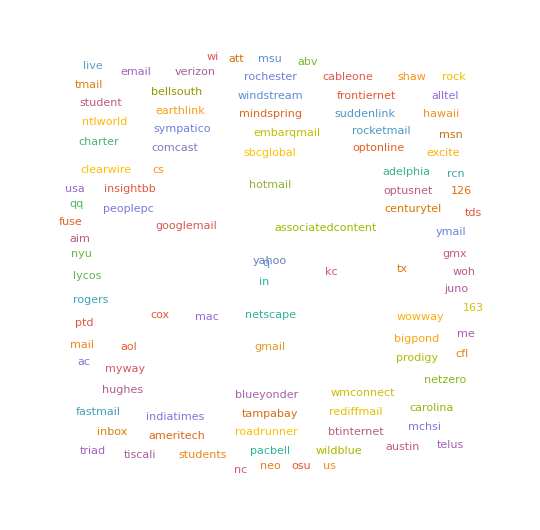

```mathematica
WordCloud[mailDomain]
```

```mathematica
LCSlist=Table[LongestCommonSubsequence[psk[[i]],usrID[[i]]],{i,Length@psk}];
```

```mathematica
LCSpos=Flatten@Position[LCSlist,x_String/;StringLength[x]>4];
```

```mathematica
LCSpsk=Cases[LCSlist,x__/;StringLength[x]>4];
```

```mathematica
Length[LCSpsk]/Length[psk] 100.3
```

3.25921

```mathematica
LCSremains=Table[StringReplace[psk[[i]],LCSlist[[i]]->""],{i,LCSpos}];
```

```mathematica
Dataset[Reverse[Sort[Counts[LCSremains]]][[;;15]]]
```